```mathematica
Null
```

```mathematica
Import[]
```

```mathematica
$Version
```

11.2.0 for Mac OS X x86 (64-bit) (June 26, 2017)

```mathematica
Import["/Users/timotheev/Downloads/compData.mx"]
```

```mathematica
?Global`*
```

```mathematica
compData
```

<|Computational aeroacoustics→<|ArticlePlaintext→17723,6,BacklinksList→{Aeroacoustic analogy,Aeroacoustics,CAA,Computational Aero Acoustics,Computational Aeroacoustics,Coolfluid,Index of physics articles (C),John Ffowcs Williams}|>,98,Computational X→<|1|>|>
 |  |  |  |

```mathematica
Dataset[compData]
```

Dataset[<>]

```mathematica
Inlinks=Map[Select[#,MemberQ[Keys@compData,#]&]&,compData[[;;,"LinksList"]]];
Inlinks = Flatten@KeyValueMap[Thread[#1-> #2]&,Inlinks];
```

```mathematica
outlinks=Map[Select[#,MemberQ[Keys@compData,#]&]&,compData[[;;,"BacklinksList"]]];
outlinks = Flatten@KeyValueMap[Thread[ #2-> #1]&,outlinks];
```

```mathematica
fullList=DeleteDuplicates[Join[Inlinks,outlinks]]
```

```mathematica
Length@fullList
```

194

```mathematica
Length@Inlinks
```

194

```mathematica
Graph[Keys@compData,Inlinks]
```

-Graphics-

```mathematica
g2 =Graph[Keys@compData,Inlinks];
```

```mathematica
CommunityGraphPlot[Graph[Keys@compData,Inlinks]]
```

-Graphics-

```mathematica
CommunityGraphPlot[Inlinks]
```

-Graphics-

```mathematica
g=Graph[Inlinks];
```

```mathematica
CommunityGraphPlot[g,FindGraphCommunities[g,Method->"Modularity"],VertexLabels->Placed["Name", Tooltip],CommunityLabels->Placed[ToString/@Range[9],Below]]
```

-Graphics-

```mathematica
CommunityWordCloud=Function[{community, links},WordCloud[StringDelete["computational"]@ToLowerCase@StringRiffle[Flatten[Apply[List,Select[links,MemberQ[community,First[#]]&&MemberQ[community,Last[#]]&],2]]],MaxItems->10,ImageSize->Tiny]]
```

Function[{community,links},WordCloud[StringDelete[computational][ToLowerCase[StringRiffle[Flatten[Apply[List,Select[links,MemberQ[community,First[#1]]&&MemberQ[community,Last[#1]]&],2]]]]],MaxItems→10,ImageSize→Tiny]]

```mathematica
CommunityGraphPlot[g,FindGraphCommunities[g,Method->"Modularity"],VertexLabels->Placed["Name", Tooltip],EdgeLabels->Placed["Name", Tooltip],CommunityLabels->Placed[(CommunityWordCloud[#,Inlinks]&/@FindGraphCommunities[g,Method->"Modularity"]),Below]]
```

-Graphics-
-Graphics-

```mathematica
Inlinks=Map[Select[#,MemberQ[Keys@compData,#]&]&,compData[[;;,"LinksList"]]];
Inlinks = Flatten@KeyValueMap[Thread[#1-> #2]&,Inlinks];
```

```mathematica
unconnected=Complement[Keys@compData,DeleteDuplicates@Flatten[List@@@Inlinks]]
```

{Computational algebra,Computational and Mathematical Organization Theory,Computational auditory scene analysis,Computational Biology Department,Computational chemical methods in solid-state physics,Computational Complexity Conference,Computational gene,Computational human phantom,Computational indistinguishability,Computational irreducibility,Computational lithography,Computational logic,Computationally enhanced craft item,Computational Materials Science,Computational methods for free surface flow,Computational musicology,Computational neurogenetic modeling,Computational RAM,Computational Resource for Drug Discovery,Computational Science Graduate Fellowship,Computational steering,Computational sustainability,Computational theology,Computational theory of mind,Computational transportation science,Computational trust}

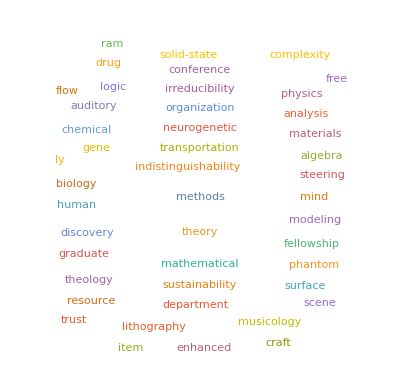

```mathematica
WordCloud[StringDelete["science"]@StringDelete["computational"]@ToLowerCase@StringRiffle[{"Computational algebra","Computational and Mathematical Organization Theory","Computational auditory scene analysis","Computational Biology Department","Computational chemical methods in solid-state physics","Computational Complexity Conference","Computational gene","Computational human phantom","Computational indistinguishability","Computational irreducibility","Computational lithography","Computational logic","Computationally enhanced craft item","Computational Materials Science","Computational methods for free surface flow","Computational musicology","Computational neurogenetic modeling","Computational RAM","Computational Resource for Drug Discovery","Computational Science Graduate Fellowship","Computational steering","Computational sustainability","Computational theology","Computational theory of mind","Computational transportation science","Computational trust"}]]
```

```mathematica
CommunityGraphPlot[g2,FindGraphCommunities[g2,Method->"Modularity"],VertexLabels->Placed["Name", Tooltip],EdgeLabels->Placed["Name", Tooltip],CommunityLabels->Placed[(CommunityWordCloud[#,Inlinks]&/@FindGraphCommunities[g2,Method->"Modularity"]),Below]]
```

-Graphics-